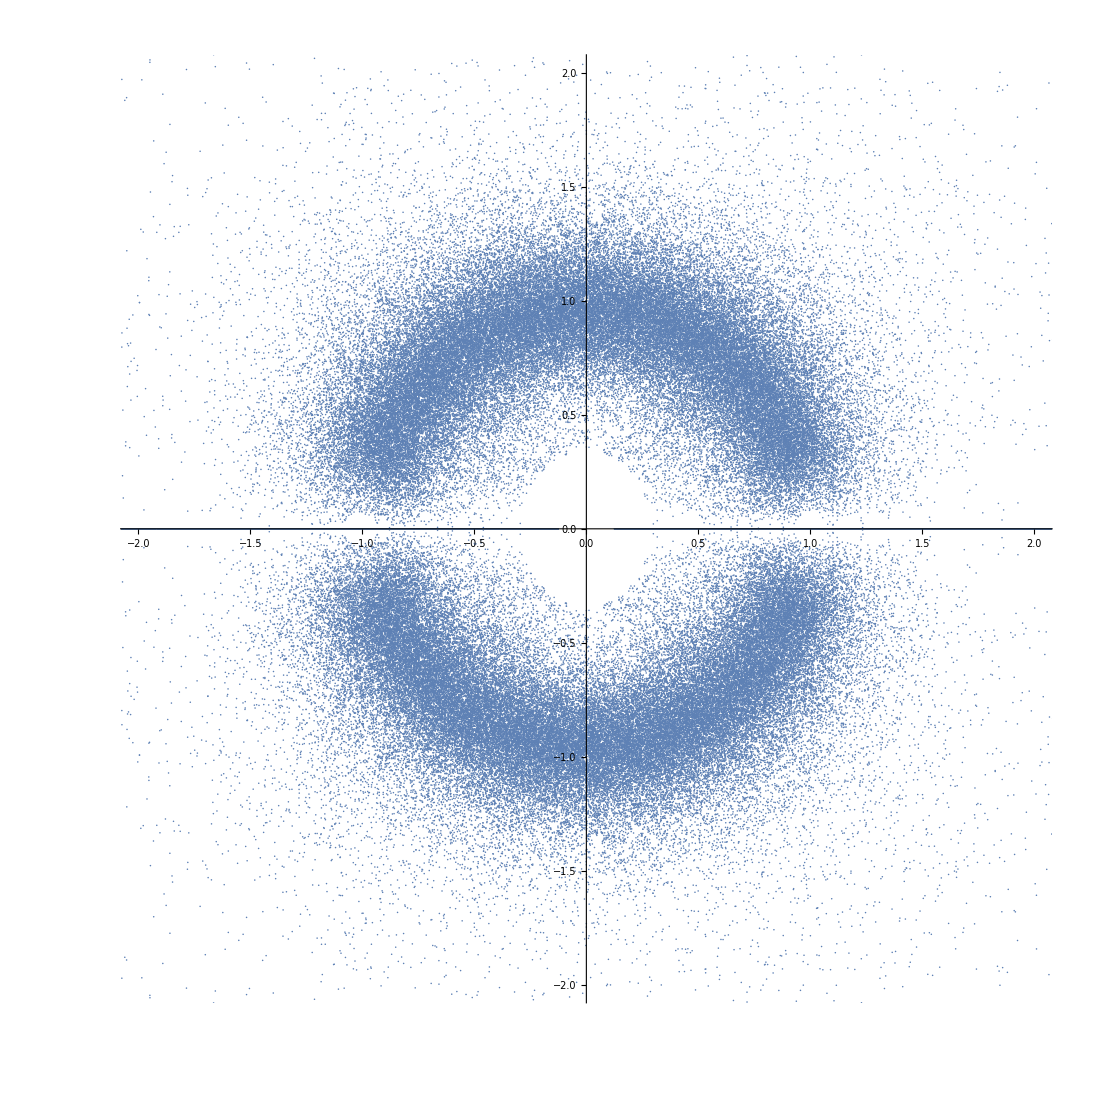

```mathematica
Clear[a]
maxDeg=10;
Cases[#,a_-> {Re@a,Im@a}]&@Quiet[
Select[#,NumberQ]&@
(Root[#1,i]& @
Sum[RandomChoice[{-7,-6,-5,-4,-3,-2,-1,1,2,3,4,5,6,7}] x^i,{i,0,maxDeg}]
	/.Partition[#,1]&@Thread[i-> Range[1,maxDeg]]//N)]&/@Range[1,20000]//Flatten[#,1]&//N//ListPlot[#,PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotStyle->PointSize[0.001]]&
```